## -Graphics- -Graphics-

```mathematica
A= {{Cos[θ],-Sin[θ]Cos[α],Sin[θ]Sin[α],a Cos[θ]},{Sin[θ], Cos[θ]Cos[α],-Cos[θ]Sin[α],a Sin[θ]},{0,Sin[α],Cos[α],d},{0,0,0,1}}
```

{{Cos[θ],-Cos[α] Sin[θ],Sin[α] Sin[θ],a Cos[θ]},{Sin[θ],Cos[α] Cos[θ],-Cos[θ] Sin[α],a Sin[θ]},{0,Sin[α],Cos[α],d},{0,0,0,1}}

```mathematica
MatrixForm[A]
```

(Cos[θ] | -Cos[α] Sin[θ] | Sin[α] Sin[θ] | a Cos[θ]
Sin[θ] | Cos[α] Cos[θ] | -Cos[θ] Sin[α] | a Sin[θ]
0 | Sin[α] | Cos[α] | d
0 | 0 | 0 | 1)

```mathematica
T1=A/. {α->-Pi/2,a->0,d->0,θ->θ1};
MatrixForm[Simplify[T1]]
```

(Cos[θ1] | 0 | -Sin[θ1] | 0
Sin[θ1] | 0 | Cos[θ1] | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
T2=A/. {α->0 ,a-> a2,d->b2,θ->θ2}
MatrixForm[Simplify[T2]]
```

{{Cos[θ2],-Sin[θ2],0,a2 Cos[θ2]},{Sin[θ2],Cos[θ2],0,a2 Sin[θ2]},{0,0,1,b2},{0,0,0,1}}

(Cos[θ2] | -Sin[θ2] | 0 | a2 Cos[θ2]
Sin[θ2] | Cos[θ2] | 0 | a2 Sin[θ2]
0 | 0 | 1 | b2
0 | 0 | 0 | 1)

```mathematica
T3=A/. {α->Pi/2,a-> a3,d->0,θ->θ3}
MatrixForm[Simplify[T3]]
```

{{Cos[θ3],0,Sin[θ3],a3 Cos[θ3]},{Sin[θ3],0,-Cos[θ3],a3 Sin[θ3]},{0,1,0,0},{0,0,0,1}}

(Cos[θ3] | 0 | Sin[θ3] | a3 Cos[θ3]
Sin[θ3] | 0 | -Cos[θ3] | a3 Sin[θ3]
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
T4=A/. {α->-Pi/2,a->0,d->b4,θ->θ4}
MatrixForm[Simplify[T4]]
```

{{Cos[θ4],0,-Sin[θ4],0},{Sin[θ4],0,Cos[θ4],0},{0,-1,0,b4},{0,0,0,1}}

(Cos[θ4] | 0 | -Sin[θ4] | 0
Sin[θ4] | 0 | Cos[θ4] | 0
0 | -1 | 0 | b4
0 | 0 | 0 | 1)

```mathematica
T5=A/. {α->Pi/2 ,a-> 0 ,d->0,θ->θ5}
MatrixForm[Simplify[T5]]
```

{{Cos[θ5],0,Sin[θ5],0},{Sin[θ5],0,-Cos[θ5],0},{0,1,0,0},{0,0,0,1}}

(Cos[θ5] | 0 | Sin[θ5] | 0
Sin[θ5] | 0 | -Cos[θ5] | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
T6=A/. {α->0,a-> 0,d->b6,θ->θ6}
MatrixForm[Simplify[T6]]
```

{{Cos[θ6],-Sin[θ6],0,0},{Sin[θ6],Cos[θ6],0,0},{0,0,1,b6},{0,0,0,1}}

(Cos[θ6] | -Sin[θ6] | 0 | 0
Sin[θ6] | Cos[θ6] | 0 | 0
0 | 0 | 1 | b6
0 | 0 | 0 | 1)

```mathematica
P2=Simplify[T1.T2]
```

{{Cos[θ1] Cos[θ2],-Cos[θ1] Sin[θ2],-Sin[θ1],a2 Cos[θ1] Cos[θ2]-b2 Sin[θ1]},{Cos[θ2] Sin[θ1],-Sin[θ1] Sin[θ2],Cos[θ1],b2 Cos[θ1]+a2 Cos[θ2] Sin[θ1]},{-Sin[θ2],-Cos[θ2],0,-a2 Sin[θ2]},{0,0,0,1}}

```mathematica
P3=Simplify[T1.T2.T3]
```

{{Cos[θ1] Cos[θ2+θ3],-Sin[θ1],Cos[θ1] Sin[θ2+θ3],Cos[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3])-b2 Sin[θ1]},{Cos[θ2+θ3] Sin[θ1],Cos[θ1],Sin[θ1] Sin[θ2+θ3],b2 Cos[θ1]+(a2 Cos[θ2]+a3 Cos[θ2+θ3]) Sin[θ1]},{-Sin[θ2+θ3],0,Cos[θ2+θ3],-a2 Sin[θ2]-a3 Sin[θ2+θ3]},{0,0,0,1}}

```mathematica
P4=Simplify[T1.T2.T3.T4]
```

{{Cos[θ1] Cos[θ2+θ3] Cos[θ4]-Sin[θ1] Sin[θ4],-Cos[θ1] Sin[θ2+θ3],-Cos[θ4] Sin[θ1]-Cos[θ1] Cos[θ2+θ3] Sin[θ4],-b2 Sin[θ1]+Cos[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3]+b4 Sin[θ2+θ3])},{Cos[θ2] Cos[θ3] Cos[θ4] Sin[θ1]-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4],-Sin[θ1] Sin[θ2+θ3],Cos[θ1] Cos[θ4]-Cos[θ2+θ3] Sin[θ1] Sin[θ4],b2 Cos[θ1]+Sin[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3]+b4 Sin[θ2+θ3])},{-Cos[θ4] Sin[θ2+θ3],-Cos[θ2+θ3],Sin[θ2+θ3] Sin[θ4],b4 Cos[θ2+θ3]-a2 Sin[θ2]-a3 Sin[θ2+θ3]},{0,0,0,1}}

```mathematica
P5=Simplify[T1.T2.T4.T5]
```

{{Cos[θ1] Cos[θ2+θ4] Cos[θ5]+Sin[θ1] Sin[θ5],-Cos[θ1] Sin[θ2+θ4],-Cos[θ5] Sin[θ1]+Cos[θ1] Cos[θ2+θ4] Sin[θ5],a2 Cos[θ1] Cos[θ2]-(b2+b4) Sin[θ1]},{Cos[θ2] Cos[θ4] Cos[θ5] Sin[θ1]-Cos[θ5] Sin[θ1] Sin[θ2] Sin[θ4]-Cos[θ1] Sin[θ5],-Sin[θ1] Sin[θ2+θ4],Cos[θ1] Cos[θ5]+Cos[θ2+θ4] Sin[θ1] Sin[θ5],(b2+b4) Cos[θ1]+a2 Cos[θ2] Sin[θ1]},{-Cos[θ5] Sin[θ2+θ4],-Cos[θ2+θ4],-Sin[θ2+θ4] Sin[θ5],-a2 Sin[θ2]},{0,0,0,1}}

```mathematica
T=Simplify[T1.T2.T3.T4.T5.T6]
MatrixForm[T]
```

{{-Sin[θ1] (Cos[θ5] Cos[θ6] Sin[θ4]+Cos[θ4] Sin[θ6])+Cos[θ1] (-Cos[θ6] Sin[θ2+θ3] Sin[θ5]+Cos[θ2+θ3] (Cos[θ4] Cos[θ5] Cos[θ6]-Sin[θ4] Sin[θ6])),Cos[θ5] Sin[θ1] Sin[θ4] Sin[θ6]-Cos[θ4] (Cos[θ6] Sin[θ1]+Cos[θ1] Cos[θ2+θ3] Cos[θ5] Sin[θ6])+Cos[θ1] (-Cos[θ2] Cos[θ3] Cos[θ6] Sin[θ4]+Cos[θ6] Sin[θ2] Sin[θ3] Sin[θ4]+Cos[θ3] Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] Sin[θ3] Sin[θ5] Sin[θ6]),-Sin[θ1] Sin[θ4] Sin[θ5]+Cos[θ1] (Cos[θ3] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ5]-Cos[θ4] Sin[θ2] Sin[θ5])),-Sin[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Cos[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5])))},{Cos[θ6] (Cos[θ5] (Cos[θ2] Cos[θ3] Cos[θ4] Sin[θ1]-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4])-Sin[θ1] Sin[θ2+θ3] Sin[θ5])+(Cos[θ1] Cos[θ4]-Cos[θ2+θ3] Sin[θ1] Sin[θ4]) Sin[θ6],Cos[θ1] (Cos[θ4] Cos[θ6]-Cos[θ5] Sin[θ4] Sin[θ6])+Sin[θ1] (-Cos[θ2+θ3] Cos[θ6] Sin[θ4]+(-Cos[θ2] Cos[θ3] Cos[θ4] Cos[θ5]+Cos[θ4] Cos[θ5] Sin[θ2] Sin[θ3]+Sin[θ2+θ3] Sin[θ5]) Sin[θ6]),Cos[θ2] Cos[θ5] Sin[θ1] Sin[θ3]+(-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4]) Sin[θ5]+Cos[θ3] Sin[θ1] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5]),Cos[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Sin[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5])))},{-Cos[θ6] (Cos[θ3] (Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ4] Cos[θ5]-Sin[θ2] Sin[θ5]))+Sin[θ2+θ3] Sin[θ4] Sin[θ6],Cos[θ3] (Cos[θ6] Sin[θ2] Sin[θ4]+(Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5]) Sin[θ6])+Sin[θ3] (-Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] (Cos[θ6] Sin[θ4]+Cos[θ4] Cos[θ5] Sin[θ6])),-Sin[θ2] (Cos[θ5] Sin[θ3]+Cos[θ3] Cos[θ4] Sin[θ5])+Cos[θ2] (Cos[θ3] Cos[θ5]-Cos[θ4] Sin[θ3] Sin[θ5]),Cos[θ2+θ3] (b4+b6 Cos[θ5])-(a2+a3 Cos[θ3]) Sin[θ2]-a3 Cos[θ2] Sin[θ3]-b6 Cos[θ4] Sin[θ2+θ3] Sin[θ5]},{0,0,0,1}}

(-Sin[θ1] (Cos[θ5] Cos[θ6] Sin[θ4]+Cos[θ4] Sin[θ6])+Cos[θ1] (-Cos[θ6] Sin[θ2+θ3] Sin[θ5]+Cos[θ2+θ3] (Cos[θ4] Cos[θ5] Cos[θ6]-Sin[θ4] Sin[θ6])) | Cos[θ5] Sin[θ1] Sin[θ4] Sin[θ6]-Cos[θ4] (Cos[θ6] Sin[θ1]+Cos[θ1] Cos[θ2+θ3] Cos[θ5] Sin[θ6])+Cos[θ1] (-Cos[θ2] Cos[θ3] Cos[θ6] Sin[θ4]+Cos[θ6] Sin[θ2] Sin[θ3] Sin[θ4]+Cos[θ3] Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] Sin[θ3] Sin[θ5] Sin[θ6]) | -Sin[θ1] Sin[θ4] Sin[θ5]+Cos[θ1] (Cos[θ3] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ5]-Cos[θ4] Sin[θ2] Sin[θ5])) | -Sin[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Cos[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5])))
Cos[θ6] (Cos[θ5] (Cos[θ2] Cos[θ3] Cos[θ4] Sin[θ1]-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4])-Sin[θ1] Sin[θ2+θ3] Sin[θ5])+(Cos[θ1] Cos[θ4]-Cos[θ2+θ3] Sin[θ1] Sin[θ4]) Sin[θ6] | Cos[θ1] (Cos[θ4] Cos[θ6]-Cos[θ5] Sin[θ4] Sin[θ6])+Sin[θ1] (-Cos[θ2+θ3] Cos[θ6] Sin[θ4]+(-Cos[θ2] Cos[θ3] Cos[θ4] Cos[θ5]+Cos[θ4] Cos[θ5] Sin[θ2] Sin[θ3]+Sin[θ2+θ3] Sin[θ5]) Sin[θ6]) | Cos[θ2] Cos[θ5] Sin[θ1] Sin[θ3]+(-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4]) Sin[θ5]+Cos[θ3] Sin[θ1] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5]) | Cos[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Sin[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5])))
-Cos[θ6] (Cos[θ3] (Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ4] Cos[θ5]-Sin[θ2] Sin[θ5]))+Sin[θ2+θ3] Sin[θ4] Sin[θ6] | Cos[θ3] (Cos[θ6] Sin[θ2] Sin[θ4]+(Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5]) Sin[θ6])+Sin[θ3] (-Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] (Cos[θ6] Sin[θ4]+Cos[θ4] Cos[θ5] Sin[θ6])) | -Sin[θ2] (Cos[θ5] Sin[θ3]+Cos[θ3] Cos[θ4] Sin[θ5])+Cos[θ2] (Cos[θ3] Cos[θ5]-Cos[θ4] Sin[θ3] Sin[θ5]) | Cos[θ2+θ3] (b4+b6 Cos[θ5])-(a2+a3 Cos[θ3]) Sin[θ2]-a3 Cos[θ2] Sin[θ3]-b6 Cos[θ4] Sin[θ2+θ3] Sin[θ5]
0 | 0 | 0 | 1)

```mathematica
Dimensions[T]
```

{4,4}

```mathematica
cm1={T1[[1,4]],T1[[2,4]],T1[[3,4]]}
```

{0,0,0}

```mathematica
cm2={P2[[1,4]],P2[[2,4]],P2[[3,4]]}
```

{a2 Cos[θ1] Cos[θ2]-b2 Sin[θ1],b2 Cos[θ1]+a2 Cos[θ2] Sin[θ1],-a2 Sin[θ2]}

```mathematica
cm3={P3[[1,4]],P3[[2,4]],P3[[3,4]]}
```

{Cos[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3])-b2 Sin[θ1],b2 Cos[θ1]+(a2 Cos[θ2]+a3 Cos[θ2+θ3]) Sin[θ1],-a2 Sin[θ2]-a3 Sin[θ2+θ3]}

```mathematica
cm4={P4[[1,4]],P4[[2,4]],P4[[3,4]]}
```

{-b2 Sin[θ1]+Cos[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3]+b4 Sin[θ2+θ3]),b2 Cos[θ1]+Sin[θ1] (a2 Cos[θ2]+a3 Cos[θ2+θ3]+b4 Sin[θ2+θ3]),b4 Cos[θ2+θ3]-a2 Sin[θ2]-a3 Sin[θ2+θ3]}

```mathematica
cm5={P5[[1,4]],P5[[2,4]],P5[[3,4]]}
```

{a2 Cos[θ1] Cos[θ2]-(b2+b4) Sin[θ1],(b2+b4) Cos[θ1]+a2 Cos[θ2] Sin[θ1],-a2 Sin[θ2]}

```mathematica
cm6={T[[1,4]],T[[2,4]],T[[3,4]]}
```

{-Sin[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Cos[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5]))),Cos[θ1] (b2+b6 Sin[θ4] Sin[θ5])+Sin[θ1] (Cos[θ2] (a2+(b4+b6 Cos[θ5]) Sin[θ3]+Cos[θ3] (a3+b6 Cos[θ4] Sin[θ5]))+Sin[θ2] (Cos[θ3] (b4+b6 Cos[θ5])-Sin[θ3] (a3+b6 Cos[θ4] Sin[θ5]))),Cos[θ2+θ3] (b4+b6 Cos[θ5])-(a2+a3 Cos[θ3]) Sin[θ2]-a3 Cos[θ2] Sin[θ3]-b6 Cos[θ4] Sin[θ2+θ3] Sin[θ5]}

```mathematica
R1p=T1⟦1;;3,1;;3⟧
```

{{Cos[θ1],0,-Sin[θ1]},{Sin[θ1],0,Cos[θ1]},{0,-1,0}}

```mathematica
R2p=P2⟦1;;3,1;;3⟧
```

{{Cos[θ1] Cos[θ2],-Cos[θ1] Sin[θ2],-Sin[θ1]},{Cos[θ2] Sin[θ1],-Sin[θ1] Sin[θ2],Cos[θ1]},{-Sin[θ2],-Cos[θ2],0}}

```mathematica
R3p=P3⟦1;;3,1;;3⟧
```

{{Cos[θ1] Cos[θ2+θ3],-Sin[θ1],Cos[θ1] Sin[θ2+θ3]},{Cos[θ2+θ3] Sin[θ1],Cos[θ1],Sin[θ1] Sin[θ2+θ3]},{-Sin[θ2+θ3],0,Cos[θ2+θ3]}}

```mathematica
R4p=P4⟦1;;3,1;;3⟧
```

{{Cos[θ1] Cos[θ2+θ3] Cos[θ4]-Sin[θ1] Sin[θ4],-Cos[θ1] Sin[θ2+θ3],-Cos[θ4] Sin[θ1]-Cos[θ1] Cos[θ2+θ3] Sin[θ4]},{Cos[θ2] Cos[θ3] Cos[θ4] Sin[θ1]-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4],-Sin[θ1] Sin[θ2+θ3],Cos[θ1] Cos[θ4]-Cos[θ2+θ3] Sin[θ1] Sin[θ4]},{-Cos[θ4] Sin[θ2+θ3],-Cos[θ2+θ3],Sin[θ2+θ3] Sin[θ4]}}

```mathematica
R5p=P5⟦1;;3,1;;3⟧
```

{{Cos[θ1] Cos[θ2+θ4] Cos[θ5]+Sin[θ1] Sin[θ5],-Cos[θ1] Sin[θ2+θ4],-Cos[θ5] Sin[θ1]+Cos[θ1] Cos[θ2+θ4] Sin[θ5]},{Cos[θ2] Cos[θ4] Cos[θ5] Sin[θ1]-Cos[θ5] Sin[θ1] Sin[θ2] Sin[θ4]-Cos[θ1] Sin[θ5],-Sin[θ1] Sin[θ2+θ4],Cos[θ1] Cos[θ5]+Cos[θ2+θ4] Sin[θ1] Sin[θ5]},{-Cos[θ5] Sin[θ2+θ4],-Cos[θ2+θ4],-Sin[θ2+θ4] Sin[θ5]}}

```mathematica
R6p=T⟦1;;3,1;;3⟧
```

{{-Sin[θ1] (Cos[θ5] Cos[θ6] Sin[θ4]+Cos[θ4] Sin[θ6])+Cos[θ1] (-Cos[θ6] Sin[θ2+θ3] Sin[θ5]+Cos[θ2+θ3] (Cos[θ4] Cos[θ5] Cos[θ6]-Sin[θ4] Sin[θ6])),Cos[θ5] Sin[θ1] Sin[θ4] Sin[θ6]-Cos[θ4] (Cos[θ6] Sin[θ1]+Cos[θ1] Cos[θ2+θ3] Cos[θ5] Sin[θ6])+Cos[θ1] (-Cos[θ2] Cos[θ3] Cos[θ6] Sin[θ4]+Cos[θ6] Sin[θ2] Sin[θ3] Sin[θ4]+Cos[θ3] Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] Sin[θ3] Sin[θ5] Sin[θ6]),-Sin[θ1] Sin[θ4] Sin[θ5]+Cos[θ1] (Cos[θ3] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ5]-Cos[θ4] Sin[θ2] Sin[θ5]))},{Cos[θ6] (Cos[θ5] (Cos[θ2] Cos[θ3] Cos[θ4] Sin[θ1]-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4])-Sin[θ1] Sin[θ2+θ3] Sin[θ5])+(Cos[θ1] Cos[θ4]-Cos[θ2+θ3] Sin[θ1] Sin[θ4]) Sin[θ6],Cos[θ1] (Cos[θ4] Cos[θ6]-Cos[θ5] Sin[θ4] Sin[θ6])+Sin[θ1] (-Cos[θ2+θ3] Cos[θ6] Sin[θ4]+(-Cos[θ2] Cos[θ3] Cos[θ4] Cos[θ5]+Cos[θ4] Cos[θ5] Sin[θ2] Sin[θ3]+Sin[θ2+θ3] Sin[θ5]) Sin[θ6]),Cos[θ2] Cos[θ5] Sin[θ1] Sin[θ3]+(-Cos[θ4] Sin[θ1] Sin[θ2] Sin[θ3]+Cos[θ1] Sin[θ4]) Sin[θ5]+Cos[θ3] Sin[θ1] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])},{-Cos[θ6] (Cos[θ3] (Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ4] Cos[θ5]-Sin[θ2] Sin[θ5]))+Sin[θ2+θ3] Sin[θ4] Sin[θ6],Cos[θ3] (Cos[θ6] Sin[θ2] Sin[θ4]+(Cos[θ4] Cos[θ5] Sin[θ2]+Cos[θ2] Sin[θ5]) Sin[θ6])+Sin[θ3] (-Sin[θ2] Sin[θ5] Sin[θ6]+Cos[θ2] (Cos[θ6] Sin[θ4]+Cos[θ4] Cos[θ5] Sin[θ6])),-Sin[θ2] (Cos[θ5] Sin[θ3]+Cos[θ3] Cos[θ4] Sin[θ5])+Cos[θ2] (Cos[θ3] Cos[θ5]-Cos[θ4] Sin[θ3] Sin[θ5])}}

```mathematica
subs={θ1->θ1[t],θ2->θ2[t],θ3->θ3[t],θ4->θ4[t],θ5->θ5[t],θ6->θ6[t]}
```

{θ1→θ1[t],θ2→θ2[t],θ3→θ3[t],θ4→θ4[t],θ5→θ5[t],θ6→θ6[t]}

```mathematica
R1pt=R1p/. subs
```

{{Cos[θ1[t]],0,-Sin[θ1[t]]},{Sin[θ1[t]],0,Cos[θ1[t]]},{0,-1,0}}

```mathematica
R2pt=R2p/. subs
```

{{Cos[θ1[t]] Cos[θ2[t]],-Cos[θ1[t]] Sin[θ2[t]],-Sin[θ1[t]]},{Cos[θ2[t]] Sin[θ1[t]],-Sin[θ1[t]] Sin[θ2[t]],Cos[θ1[t]]},{-Sin[θ2[t]],-Cos[θ2[t]],0}}

```mathematica
R3pt=R3p/. subs
```

{{Cos[θ1[t]] Cos[θ2[t]+θ3[t]],-Sin[θ1[t]],Cos[θ1[t]] Sin[θ2[t]+θ3[t]]},{Cos[θ2[t]+θ3[t]] Sin[θ1[t]],Cos[θ1[t]],Sin[θ1[t]] Sin[θ2[t]+θ3[t]]},{-Sin[θ2[t]+θ3[t]],0,Cos[θ2[t]+θ3[t]]}}

```mathematica
R4pt=R4p/. subs
```

{{Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ4[t]]-Sin[θ1[t]] Sin[θ4[t]],-Cos[θ1[t]] Sin[θ2[t]+θ3[t]],-Cos[θ4[t]] Sin[θ1[t]]-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ4[t]]},{Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]]-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]],-Sin[θ1[t]] Sin[θ2[t]+θ3[t]],Cos[θ1[t]] Cos[θ4[t]]-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] Sin[θ4[t]]},{-Cos[θ4[t]] Sin[θ2[t]+θ3[t]],-Cos[θ2[t]+θ3[t]],Sin[θ2[t]+θ3[t]] Sin[θ4[t]]}}

```mathematica
R5pt=R5p/. subs
```

{{Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Cos[θ5[t]]+Sin[θ1[t]] Sin[θ5[t]],-Cos[θ1[t]] Sin[θ2[t]+θ4[t]],-Cos[θ5[t]] Sin[θ1[t]]+Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Sin[θ5[t]]},{Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ1[t]]-Cos[θ5[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ4[t]]-Cos[θ1[t]] Sin[θ5[t]],-Sin[θ1[t]] Sin[θ2[t]+θ4[t]],Cos[θ1[t]] Cos[θ5[t]]+Cos[θ2[t]+θ4[t]] Sin[θ1[t]] Sin[θ5[t]]},{-Cos[θ5[t]] Sin[θ2[t]+θ4[t]],-Cos[θ2[t]+θ4[t]],-Sin[θ2[t]+θ4[t]] Sin[θ5[t]]}}

```mathematica
R6pt=R6p/. subs
```

{{-Sin[θ1[t]] (Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Sin[θ6[t]])+Cos[θ1[t]] (-Cos[θ6[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]]+Cos[θ2[t]+θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]]-Sin[θ4[t]] Sin[θ6[t]])),Cos[θ5[t]] Sin[θ1[t]] Sin[θ4[t]] Sin[θ6[t]]-Cos[θ4[t]] (Cos[θ6[t]] Sin[θ1[t]]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Sin[θ6[t]])+Cos[θ1[t]] (-Cos[θ2[t]] Cos[θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ6[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]]+Cos[θ3[t]] Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]]+Cos[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] Sin[θ6[t]]),-Sin[θ1[t]] Sin[θ4[t]] Sin[θ5[t]]+Cos[θ1[t]] (Cos[θ3[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]]))},{Cos[θ6[t]] (Cos[θ5[t]] (Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]]-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]])-Sin[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]])+(Cos[θ1[t]] Cos[θ4[t]]-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] Sin[θ4[t]]) Sin[θ6[t]],Cos[θ1[t]] (Cos[θ4[t]] Cos[θ6[t]]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]])+Sin[θ1[t]] (-Cos[θ2[t]+θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+(-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) Sin[θ6[t]]),Cos[θ2[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ3[t]]+(-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]]) Sin[θ5[t]]+Cos[θ3[t]] Sin[θ1[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]])},{-Cos[θ6[t]] (Cos[θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]]-Sin[θ2[t]] Sin[θ5[t]]))+Sin[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ6[t]],Cos[θ3[t]] (Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]]+(Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) Sin[θ6[t]])+Sin[θ3[t]] (-Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]]+Cos[θ2[t]] (Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]])),-Sin[θ2[t]] (Cos[θ5[t]] Sin[θ3[t]]+Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]])+Cos[θ2[t]] (Cos[θ3[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ3[t]] Sin[θ5[t]])}}

```mathematica
dR1=D[R1pt,t]
```

{{-Sin[θ1[t]] θ1'[t],0,-Cos[θ1[t]] θ1'[t]},{Cos[θ1[t]] θ1'[t],0,-Sin[θ1[t]] θ1'[t]},{0,0,0}}

```mathematica
dR2=D[R2pt,t]
```

{{-Cos[θ2[t]] Sin[θ1[t]] θ1'[t]-Cos[θ1[t]] Sin[θ2[t]] θ2'[t],Sin[θ1[t]] Sin[θ2[t]] θ1'[t]-Cos[θ1[t]] Cos[θ2[t]] θ2'[t],-Cos[θ1[t]] θ1'[t]},{Cos[θ1[t]] Cos[θ2[t]] θ1'[t]-Sin[θ1[t]] Sin[θ2[t]] θ2'[t],-Cos[θ1[t]] Sin[θ2[t]] θ1'[t]-Cos[θ2[t]] Sin[θ1[t]] θ2'[t],-Sin[θ1[t]] θ1'[t]},{-Cos[θ2[t]] θ2'[t],Sin[θ2[t]] θ2'[t],0}}

```mathematica
dR3=D[R3pt,t]
```

{{-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] θ1'[t]-Cos[θ1[t]] Sin[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t]),-Cos[θ1[t]] θ1'[t],-Sin[θ1[t]] Sin[θ2[t]+θ3[t]] θ1'[t]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t])},{Cos[θ1[t]] Cos[θ2[t]+θ3[t]] θ1'[t]-Sin[θ1[t]] Sin[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t]),-Sin[θ1[t]] θ1'[t],Cos[θ1[t]] Sin[θ2[t]+θ3[t]] θ1'[t]+Cos[θ2[t]+θ3[t]] Sin[θ1[t]] (θ2'[t]+θ3'[t])},{-Cos[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t]),0,-Sin[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t])}}

```mathematica
dR4=D[R4pt,t]
```

{{-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ1[t]] θ1'[t]-Cos[θ1[t]] Sin[θ4[t]] θ1'[t]-Cos[θ1[t]] Cos[θ4[t]] Sin[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t])-Cos[θ4[t]] Sin[θ1[t]] θ4'[t]-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ4[t]] θ4'[t],Sin[θ1[t]] Sin[θ2[t]+θ3[t]] θ1'[t]-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t]),-Cos[θ1[t]] Cos[θ4[t]] θ1'[t]+Cos[θ2[t]+θ3[t]] Sin[θ1[t]] Sin[θ4[t]] θ1'[t]+Cos[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ4[t]] θ4'[t]+Sin[θ1[t]] Sin[θ4[t]] θ4'[t]},{Cos[θ1[t]] Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] θ1'[t]-Cos[θ1[t]] Cos[θ4[t]] Sin[θ2[t]] Sin[θ3[t]] θ1'[t]-Sin[θ1[t]] Sin[θ4[t]] θ1'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] θ2'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ3[t]] θ2'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] θ3'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ3[t]] θ3'[t]+Cos[θ1[t]] Cos[θ4[t]] θ4'[t]-Cos[θ2[t]] Cos[θ3[t]] Sin[θ1[t]] Sin[θ4[t]] θ4'[t]+Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] θ4'[t],-Cos[θ1[t]] Sin[θ2[t]+θ3[t]] θ1'[t]-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] (θ2'[t]+θ3'[t]),-Cos[θ4[t]] Sin[θ1[t]] θ1'[t]-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]+Sin[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ1[t]] θ4'[t]-Cos[θ1[t]] Sin[θ4[t]] θ4'[t]},{-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] (θ2'[t]+θ3'[t])+Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ4'[t],Sin[θ2[t]+θ3[t]] (θ2'[t]+θ3'[t]),Cos[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])+Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ4'[t]}}

```mathematica
dR5=D[R5pt,t]
```

{{-Cos[θ2[t]+θ4[t]] Cos[θ5[t]] Sin[θ1[t]] θ1'[t]+Cos[θ1[t]] Sin[θ5[t]] θ1'[t]-Cos[θ1[t]] Cos[θ5[t]] Sin[θ2[t]+θ4[t]] (θ2'[t]+θ4'[t])+Cos[θ5[t]] Sin[θ1[t]] θ5'[t]-Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Sin[θ5[t]] θ5'[t],Sin[θ1[t]] Sin[θ2[t]+θ4[t]] θ1'[t]-Cos[θ1[t]] Cos[θ2[t]+θ4[t]] (θ2'[t]+θ4'[t]),-Cos[θ1[t]] Cos[θ5[t]] θ1'[t]-Cos[θ2[t]+θ4[t]] Sin[θ1[t]] Sin[θ5[t]] θ1'[t]-Cos[θ1[t]] Sin[θ2[t]+θ4[t]] Sin[θ5[t]] (θ2'[t]+θ4'[t])+Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Cos[θ5[t]] θ5'[t]+Sin[θ1[t]] Sin[θ5[t]] θ5'[t]},{Cos[θ1[t]] Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] θ1'[t]-Cos[θ1[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ4[t]] θ1'[t]+Sin[θ1[t]] Sin[θ5[t]] θ1'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ2[t]] θ2'[t]-Cos[θ2[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ4[t]] θ2'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ2[t]] θ4'[t]-Cos[θ2[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ4[t]] θ4'[t]-Cos[θ1[t]] Cos[θ5[t]] θ5'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ5[t]] θ5'[t]+Sin[θ1[t]] Sin[θ2[t]] Sin[θ4[t]] Sin[θ5[t]] θ5'[t],-Cos[θ1[t]] Sin[θ2[t]+θ4[t]] θ1'[t]-Cos[θ2[t]+θ4[t]] Sin[θ1[t]] (θ2'[t]+θ4'[t]),-Cos[θ5[t]] Sin[θ1[t]] θ1'[t]+Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]-Sin[θ1[t]] Sin[θ2[t]+θ4[t]] Sin[θ5[t]] (θ2'[t]+θ4'[t])+Cos[θ2[t]+θ4[t]] Cos[θ5[t]] Sin[θ1[t]] θ5'[t]-Cos[θ1[t]] Sin[θ5[t]] θ5'[t]},{-Cos[θ2[t]+θ4[t]] Cos[θ5[t]] (θ2'[t]+θ4'[t])+Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ5'[t],Sin[θ2[t]+θ4[t]] (θ2'[t]+θ4'[t]),-Cos[θ2[t]+θ4[t]] Sin[θ5[t]] (θ2'[t]+θ4'[t])-Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ5'[t]}}

```mathematica
dR6=D[R6pt,t]
```

{{-Cos[θ1[t]] (Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Sin[θ6[t]]) θ1'[t]-Sin[θ1[t]] (-Cos[θ6[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]]+Cos[θ2[t]+θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]]-Sin[θ4[t]] Sin[θ6[t]])) θ1'[t]-Sin[θ1[t]] (Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]] θ4'[t]-Sin[θ4[t]] Sin[θ6[t]] θ4'[t]-Cos[θ6[t]] Sin[θ4[t]] Sin[θ5[t]] θ5'[t]+Cos[θ4[t]] Cos[θ6[t]] θ6'[t]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t])+Cos[θ1[t]] (-Cos[θ2[t]+θ3[t]] Cos[θ6[t]] Sin[θ5[t]] (θ2'[t]+θ3'[t])-Sin[θ2[t]+θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]]-Sin[θ4[t]] Sin[θ6[t]]) (θ2'[t]+θ3'[t])-Cos[θ5[t]] Cos[θ6[t]] Sin[θ2[t]+θ3[t]] θ5'[t]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ6'[t]+Cos[θ2[t]+θ3[t]] (-Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]] θ4'[t]-Cos[θ4[t]] Sin[θ6[t]] θ4'[t]-Cos[θ4[t]] Cos[θ6[t]] Sin[θ5[t]] θ5'[t]-Cos[θ6[t]] Sin[θ4[t]] θ6'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]] θ6'[t])),Cos[θ1[t]] Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]] θ1'[t]-Sin[θ1[t]] (-Cos[θ2[t]] Cos[θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ6[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]]+Cos[θ3[t]] Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]]+Cos[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] Sin[θ6[t]]) θ1'[t]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ6[t]] θ4'[t]+Sin[θ4[t]] (Cos[θ6[t]] Sin[θ1[t]]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Sin[θ6[t]]) θ4'[t]-Sin[θ1[t]] Sin[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+Cos[θ5[t]] Cos[θ6[t]] Sin[θ1[t]] Sin[θ4[t]] θ6'[t]-Cos[θ4[t]] (Cos[θ1[t]] Cos[θ6[t]] θ1'[t]-Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ6[t]] θ1'[t]-Cos[θ1[t]] Cos[θ5[t]] Sin[θ2[t]+θ3[t]] Sin[θ6[t]] (θ2'[t]+θ3'[t])-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Cos[θ6[t]] θ6'[t]-Sin[θ1[t]] Sin[θ6[t]] θ6'[t])+Cos[θ1[t]] (Cos[θ3[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]] θ2'[t]+Cos[θ2[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ4[t]] θ2'[t]+Cos[θ2[t]] Cos[θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ2'[t]-Sin[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ2'[t]+Cos[θ3[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]] θ3'[t]+Cos[θ2[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ4[t]] θ3'[t]+Cos[θ2[t]] Cos[θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ3'[t]-Sin[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ3'[t]-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ6[t]] θ4'[t]+Cos[θ4[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ3[t]] θ4'[t]+Cos[θ3[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ6[t]] θ5'[t]+Cos[θ2[t]] Cos[θ5[t]] Sin[θ3[t]] Sin[θ6[t]] θ5'[t]+Cos[θ3[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] Cos[θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t]-Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t]),-Cos[θ1[t]] Sin[θ4[t]] Sin[θ5[t]] θ1'[t]-Sin[θ1[t]] (Cos[θ3[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]])) θ1'[t]-Cos[θ4[t]] Sin[θ1[t]] Sin[θ5[t]] θ4'[t]-Cos[θ5[t]] Sin[θ1[t]] Sin[θ4[t]] θ5'[t]+Cos[θ1[t]] (-Sin[θ3[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]]) θ3'[t]+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]]) θ3'[t]+Sin[θ3[t]] (-Cos[θ5[t]] Sin[θ2[t]] θ2'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]] θ2'[t]+Sin[θ2[t]] Sin[θ4[t]] Sin[θ5[t]] θ4'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] θ5'[t]-Cos[θ2[t]] Sin[θ5[t]] θ5'[t])+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ5[t]] θ2'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]] θ2'[t]-Cos[θ2[t]] Sin[θ4[t]] Sin[θ5[t]] θ4'[t]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] θ5'[t]-Sin[θ2[t]] Sin[θ5[t]] θ5'[t]))},{Sin[θ6[t]] (-Cos[θ4[t]] Sin[θ1[t]] θ1'[t]-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]+Sin[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ1[t]] θ4'[t]-Cos[θ1[t]] Sin[θ4[t]] θ4'[t])+Cos[θ6[t]] (-Cos[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]] θ1'[t]-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] Sin[θ5[t]] (θ2'[t]+θ3'[t])+Cos[θ5[t]] (Cos[θ1[t]] Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] θ1'[t]-Cos[θ1[t]] Cos[θ4[t]] Sin[θ2[t]] Sin[θ3[t]] θ1'[t]-Sin[θ1[t]] Sin[θ4[t]] θ1'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] θ2'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ3[t]] θ2'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] θ3'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ3[t]] θ3'[t]+Cos[θ1[t]] Cos[θ4[t]] θ4'[t]-Cos[θ2[t]] Cos[θ3[t]] Sin[θ1[t]] Sin[θ4[t]] θ4'[t]+Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] θ4'[t])-Cos[θ5[t]] Sin[θ1[t]] Sin[θ2[t]+θ3[t]] θ5'[t]-(Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]]-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]]) Sin[θ5[t]] θ5'[t])+Cos[θ6[t]] (Cos[θ1[t]] Cos[θ4[t]]-Cos[θ2[t]+θ3[t]] Sin[θ1[t]] Sin[θ4[t]]) θ6'[t]-(Cos[θ5[t]] (Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]]-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]])-Sin[θ1[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) Sin[θ6[t]] θ6'[t],-Sin[θ1[t]] (Cos[θ4[t]] Cos[θ6[t]]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]]) θ1'[t]+Cos[θ1[t]] (-Cos[θ2[t]+θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+(-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) Sin[θ6[t]]) θ1'[t]+Cos[θ1[t]] (-Cos[θ6[t]] Sin[θ4[t]] θ4'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]] θ4'[t]+Sin[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]-Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]] θ6'[t]-Cos[θ4[t]] Sin[θ6[t]] θ6'[t])+Sin[θ1[t]] (Cos[θ6[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Cos[θ6[t]] θ4'[t]+Sin[θ6[t]] (Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] θ2'[t]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]] θ2'[t]+Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] θ3'[t]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]] θ3'[t]+Cos[θ2[t]+θ3[t]] Sin[θ5[t]] (θ2'[t]+θ3'[t])+Cos[θ2[t]] Cos[θ3[t]] Cos[θ5[t]] Sin[θ4[t]] θ4'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] θ4'[t]+Cos[θ5[t]] Sin[θ2[t]+θ3[t]] θ5'[t]+Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]] θ5'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] θ5'[t])+Cos[θ6[t]] (-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) θ6'[t]+Cos[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t]),Cos[θ1[t]] Cos[θ2[t]] Cos[θ5[t]] Sin[θ3[t]] θ1'[t]+Cos[θ1[t]] Cos[θ3[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]]) θ1'[t]-Cos[θ5[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]] θ2'[t]+Cos[θ2[t]] Cos[θ3[t]] Cos[θ5[t]] Sin[θ1[t]] θ3'[t]-Sin[θ1[t]] Sin[θ3[t]] (Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]]) θ3'[t]+Sin[θ5[t]] (-Cos[θ1[t]] Cos[θ4[t]] Sin[θ2[t]] Sin[θ3[t]] θ1'[t]-Sin[θ1[t]] Sin[θ4[t]] θ1'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ3[t]] θ2'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] θ3'[t]+Cos[θ1[t]] Cos[θ4[t]] θ4'[t]+Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] θ4'[t])+Cos[θ5[t]] (-Cos[θ4[t]] Sin[θ1[t]] Sin[θ2[t]] Sin[θ3[t]]+Cos[θ1[t]] Sin[θ4[t]]) θ5'[t]-Cos[θ2[t]] Sin[θ1[t]] Sin[θ3[t]] Sin[θ5[t]] θ5'[t]+Cos[θ3[t]] Sin[θ1[t]] (Cos[θ2[t]] Cos[θ5[t]] θ2'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]] θ2'[t]-Cos[θ2[t]] Sin[θ4[t]] Sin[θ5[t]] θ4'[t]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] θ5'[t]-Sin[θ2[t]] Sin[θ5[t]] θ5'[t])},{Cos[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ6[t]] (θ2'[t]+θ3'[t])+Cos[θ4[t]] Sin[θ2[t]+θ3[t]] Sin[θ6[t]] θ4'[t]-Cos[θ6[t]] (-Sin[θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) θ3'[t]+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]]-Sin[θ2[t]] Sin[θ5[t]]) θ3'[t]+Sin[θ3[t]] (-Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] θ2'[t]-Cos[θ2[t]] Sin[θ5[t]] θ2'[t]-Cos[θ2[t]] Cos[θ5[t]] Sin[θ4[t]] θ4'[t]-Cos[θ5[t]] Sin[θ2[t]] θ5'[t]-Cos[θ2[t]] Cos[θ4[t]] Sin[θ5[t]] θ5'[t])+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] θ2'[t]-Sin[θ2[t]] Sin[θ5[t]] θ2'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ4[t]] θ4'[t]+Cos[θ2[t]] Cos[θ5[t]] θ5'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]] θ5'[t]))+Cos[θ6[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ6'[t]+(Cos[θ3[t]] (Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]]-Sin[θ2[t]] Sin[θ5[t]])) Sin[θ6[t]] θ6'[t],-Sin[θ3[t]] (Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]]+(Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) Sin[θ6[t]]) θ3'[t]+Cos[θ3[t]] (-Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]]+Cos[θ2[t]] (Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]])) θ3'[t]+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ6[t]] Sin[θ4[t]] θ2'[t]+Cos[θ4[t]] Cos[θ6[t]] Sin[θ2[t]] θ4'[t]+Sin[θ6[t]] (Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] θ2'[t]-Sin[θ2[t]] Sin[θ5[t]] θ2'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ4[t]] θ4'[t]+Cos[θ2[t]] Cos[θ5[t]] θ5'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]] θ5'[t])+Cos[θ6[t]] (Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) θ6'[t]-Sin[θ2[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t])+Sin[θ3[t]] (-Cos[θ2[t]] Sin[θ5[t]] Sin[θ6[t]] θ2'[t]-Sin[θ2[t]] (Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]]) θ2'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ6[t]] θ5'[t]-Cos[θ6[t]] Sin[θ2[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] (Cos[θ4[t]] Cos[θ6[t]] θ4'[t]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]] θ4'[t]-Cos[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]] θ6'[t]-Sin[θ4[t]] Sin[θ6[t]] θ6'[t])),-Cos[θ2[t]] (Cos[θ5[t]] Sin[θ3[t]]+Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]]) θ2'[t]-Sin[θ2[t]] (Cos[θ3[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ3[t]] Sin[θ5[t]]) θ2'[t]+Cos[θ2[t]] (-Cos[θ5[t]] Sin[θ3[t]] θ3'[t]-Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]] θ3'[t]+Sin[θ3[t]] Sin[θ4[t]] Sin[θ5[t]] θ4'[t]-Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]] θ5'[t]-Cos[θ3[t]] Sin[θ5[t]] θ5'[t])-Sin[θ2[t]] (Cos[θ3[t]] Cos[θ5[t]] θ3'[t]-Cos[θ4[t]] Sin[θ3[t]] Sin[θ5[t]] θ3'[t]-Cos[θ3[t]] Sin[θ4[t]] Sin[θ5[t]] θ4'[t]+Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] θ5'[t]-Sin[θ3[t]] Sin[θ5[t]] θ5'[t])}}

```mathematica
Dimensions[dR6]
```

{3,3}

```mathematica
Ω1=Simplify[Transpose[R1pt].dR1]
MatrixForm[Ω1]
Ω2=Simplify[Transpose[R2pt].dR2]
MatrixForm[Ω2]
Ω3=Simplify[Transpose[R3pt].dR3]
MatrixForm[Ω3]
Ω4=Simplify[Transpose[R4pt].dR4]
MatrixForm[Ω4]
Ω5=Simplify[Transpose[R5pt].dR5]
MatrixForm[Ω5]
Ω6=Simplify[Transpose[R5pt].dR6]
MatrixForm[Ω6]
```

{{0,0,-θ1'[t]},{0,0,0},{θ1'[t],0,0}}

(0 | 0 | -θ1'[t]
0 | 0 | 0
θ1'[t] | 0 | 0)

{{0,-θ2'[t],-Cos[θ2[t]] θ1'[t]},{θ2'[t],0,Sin[θ2[t]] θ1'[t]},{Cos[θ2[t]] θ1'[t],-Sin[θ2[t]] θ1'[t],0}}

(0 | -θ2'[t] | -Cos[θ2[t]] θ1'[t]
θ2'[t] | 0 | Sin[θ2[t]] θ1'[t]
Cos[θ2[t]] θ1'[t] | -Sin[θ2[t]] θ1'[t] | 0)

{{0,-Cos[θ2[t]+θ3[t]] θ1'[t],θ2'[t]+θ3'[t]},{Cos[θ2[t]+θ3[t]] θ1'[t],0,Sin[θ2[t]+θ3[t]] θ1'[t]},{-θ2'[t]-θ3'[t],-Sin[θ2[t]+θ3[t]] θ1'[t],0}}

(0 | -Cos[θ2[t]+θ3[t]] θ1'[t] | θ2'[t]+θ3'[t]
Cos[θ2[t]+θ3[t]] θ1'[t] | 0 | Sin[θ2[t]+θ3[t]] θ1'[t]
-θ2'[t]-θ3'[t] | -Sin[θ2[t]+θ3[t]] θ1'[t] | 0)

{{0,-Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]-Cos[θ4[t]] (θ2'[t]+θ3'[t]),-Cos[θ2[t]+θ3[t]] θ1'[t]-θ4'[t]},{Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]+Cos[θ4[t]] (θ2'[t]+θ3'[t]),0,Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ1'[t]-Sin[θ4[t]] (θ2'[t]+θ3'[t])},{Cos[θ2[t]+θ3[t]] θ1'[t]+θ4'[t],-Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ1'[t]+Sin[θ4[t]] (θ2'[t]+θ3'[t]),0}}

(0 | -Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]-Cos[θ4[t]] (θ2'[t]+θ3'[t]) | -Cos[θ2[t]+θ3[t]] θ1'[t]-θ4'[t]
Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]+Cos[θ4[t]] (θ2'[t]+θ3'[t]) | 0 | Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ1'[t]-Sin[θ4[t]] (θ2'[t]+θ3'[t])
Cos[θ2[t]+θ3[t]] θ1'[t]+θ4'[t] | -Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ1'[t]+Sin[θ4[t]] (θ2'[t]+θ3'[t]) | 0)

{{0,Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]-Cos[θ5[t]] (θ2'[t]+θ4'[t]),-Cos[θ2[t]+θ4[t]] θ1'[t]+θ5'[t]},{-Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]+Cos[θ5[t]] (θ2'[t]+θ4'[t]),0,Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ1'[t]+Sin[θ5[t]] (θ2'[t]+θ4'[t])},{Cos[θ2[t]+θ4[t]] θ1'[t]-θ5'[t],-Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ1'[t]-Sin[θ5[t]] (θ2'[t]+θ4'[t]),0}}

(0 | Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]-Cos[θ5[t]] (θ2'[t]+θ4'[t]) | -Cos[θ2[t]+θ4[t]] θ1'[t]+θ5'[t]
-Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]+Cos[θ5[t]] (θ2'[t]+θ4'[t]) | 0 | Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ1'[t]+Sin[θ5[t]] (θ2'[t]+θ4'[t])
Cos[θ2[t]+θ4[t]] θ1'[t]-θ5'[t] | -Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ1'[t]-Sin[θ5[t]] (θ2'[t]+θ4'[t]) | 0)

```mathematica
Dimensions[Ω6]
```

{3,3}

```mathematica
ω1={Ω1⟦3,2⟧,Ω1⟦1,3⟧,Ω1⟦2,1⟧}
ω2={Ω2⟦3,2⟧,Ω2⟦1,3⟧,Ω2⟦2,1⟧}
ω3={Ω3⟦3,2⟧,Ω3⟦1,3⟧,Ω3⟦2,1⟧}
ω4={Ω4⟦3,2⟧,Ω4⟦1,3⟧,Ω4⟦2,1⟧}
ω5={Ω5⟦3,2⟧,Ω5⟦1,3⟧,Ω5⟦2,1⟧}
ω6={Ω6⟦3,2⟧,Ω6⟦1,3⟧,Ω6⟦2,1⟧}
```

{0,-θ1'[t],0}

{-Sin[θ2[t]] θ1'[t],-Cos[θ2[t]] θ1'[t],θ2'[t]}

{-Sin[θ2[t]+θ3[t]] θ1'[t],θ2'[t]+θ3'[t],Cos[θ2[t]+θ3[t]] θ1'[t]}

{-Cos[θ4[t]] Sin[θ2[t]+θ3[t]] θ1'[t]+Sin[θ4[t]] (θ2'[t]+θ3'[t]),-Cos[θ2[t]+θ3[t]] θ1'[t]-θ4'[t],Sin[θ2[t]+θ3[t]] Sin[θ4[t]] θ1'[t]+Cos[θ4[t]] (θ2'[t]+θ3'[t])}

{-Cos[θ5[t]] Sin[θ2[t]+θ4[t]] θ1'[t]-Sin[θ5[t]] (θ2'[t]+θ4'[t]),-Cos[θ2[t]+θ4[t]] θ1'[t]+θ5'[t],-Sin[θ2[t]+θ4[t]] Sin[θ5[t]] θ1'[t]+Cos[θ5[t]] (θ2'[t]+θ4'[t])}

{(-Cos[θ5[t]] Sin[θ1[t]]+Cos[θ1[t]] Cos[θ2[t]+θ4[t]] Sin[θ5[t]]) (Cos[θ1[t]] Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]] θ1'[t]-Sin[θ1[t]] (Sin[θ2[t]] (Cos[θ6[t]] Sin[θ3[t]] Sin[θ4[t]]+Cos[θ3[t]] Sin[θ5[t]] Sin[θ6[t]])+Cos[θ2[t]] (-Cos[θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+Sin[θ3[t]] Sin[θ5[t]] Sin[θ6[t]])) θ1'[t]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ6[t]] θ4'[t]+Sin[θ4[t]] (Cos[θ6[t]] Sin[θ1[t]]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Sin[θ6[t]]) θ4'[t]-Sin[θ1[t]] Sin[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+Cos[θ5[t]] Cos[θ6[t]] Sin[θ1[t]] Sin[θ4[t]] θ6'[t]-Cos[θ4[t]] (Cos[θ1[t]] Cos[θ6[t]] θ1'[t]-Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Sin[θ1[t]] Sin[θ6[t]] θ1'[t]-Cos[θ1[t]] Cos[θ5[t]] Sin[θ2[t]+θ3[t]] Sin[θ6[t]] (θ2'[t]+θ3'[t])-Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+Cos[θ1[t]] Cos[θ2[t]+θ3[t]] Cos[θ5[t]] Cos[θ6[t]] θ6'[t]-Sin[θ1[t]] Sin[θ6[t]] θ6'[t])+Cos[θ1[t]] ((Cos[θ3[t]] (Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]]+Cos[θ2[t]] Sin[θ5[t]] Sin[θ6[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ6[t]] Sin[θ4[t]]-Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]])) θ2'[t]+(Cos[θ3[t]] (Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]]+Cos[θ2[t]] Sin[θ5[t]] Sin[θ6[t]])+Sin[θ3[t]] (Cos[θ2[t]] Cos[θ6[t]] Sin[θ4[t]]-Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]])) θ3'[t]-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ6[t]] θ4'[t]+Cos[θ4[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ3[t]] θ4'[t]+Cos[θ3[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ6[t]] θ5'[t]+Cos[θ2[t]] Cos[θ5[t]] Sin[θ3[t]] Sin[θ6[t]] θ5'[t]+Cos[θ3[t]] Cos[θ6[t]] Sin[θ2[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] Cos[θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t]-Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t]))+(Cos[θ1[t]] Cos[θ5[t]]+Cos[θ2[t]+θ4[t]] Sin[θ1[t]] Sin[θ5[t]]) (-Sin[θ1[t]] (Cos[θ4[t]] Cos[θ6[t]]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]]) θ1'[t]+Cos[θ1[t]] (-Cos[θ2[t]+θ3[t]] Cos[θ6[t]] Sin[θ4[t]]+(-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) Sin[θ6[t]]) θ1'[t]+Sin[θ1[t]] (Cos[θ6[t]] Sin[θ2[t]+θ3[t]] Sin[θ4[t]] (θ2'[t]+θ3'[t])-Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Cos[θ6[t]] θ4'[t]+Sin[θ6[t]] ((Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]]+Cos[θ2[t]+θ3[t]] Sin[θ5[t]]) θ2'[t]+(Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]]+Cos[θ2[t]+θ3[t]] Sin[θ5[t]]) θ3'[t]+Cos[θ2[t]] Cos[θ3[t]] Cos[θ5[t]] Sin[θ4[t]] θ4'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] θ4'[t]+Cos[θ5[t]] Sin[θ2[t]+θ3[t]] θ5'[t]+Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]] θ5'[t]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ3[t]] Sin[θ5[t]] θ5'[t])+Cos[θ6[t]] (-Cos[θ2[t]] Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]] Sin[θ3[t]]+Sin[θ2[t]+θ3[t]] Sin[θ5[t]]) θ6'[t]+Cos[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t])-Cos[θ1[t]] ((Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]]) θ4'[t]-Sin[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+(Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Sin[θ6[t]]) θ6'[t]))-Sin[θ2[t]+θ4[t]] Sin[θ5[t]] (-Sin[θ3[t]] (Cos[θ6[t]] Sin[θ2[t]] Sin[θ4[t]]+(Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) Sin[θ6[t]]) θ3'[t]+Cos[θ3[t]] (-Sin[θ2[t]] Sin[θ5[t]] Sin[θ6[t]]+Cos[θ2[t]] (Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]])) θ3'[t]+Cos[θ3[t]] (Cos[θ2[t]] Cos[θ6[t]] Sin[θ4[t]] θ2'[t]+Cos[θ4[t]] Cos[θ6[t]] Sin[θ2[t]] θ4'[t]+Sin[θ6[t]] ((Cos[θ2[t]] Cos[θ4[t]] Cos[θ5[t]]-Sin[θ2[t]] Sin[θ5[t]]) θ2'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ4[t]] θ4'[t]+(Cos[θ2[t]] Cos[θ5[t]]-Cos[θ4[t]] Sin[θ2[t]] Sin[θ5[t]]) θ5'[t])+Cos[θ6[t]] (Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]]+Cos[θ2[t]] Sin[θ5[t]]) θ6'[t]-Sin[θ2[t]] Sin[θ4[t]] Sin[θ6[t]] θ6'[t])+Sin[θ3[t]] (-Cos[θ2[t]] Sin[θ5[t]] Sin[θ6[t]] θ2'[t]-Sin[θ2[t]] (Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Cos[θ5[t]] Sin[θ6[t]]) θ2'[t]-Cos[θ5[t]] Sin[θ2[t]] Sin[θ6[t]] θ5'[t]-Cos[θ6[t]] Sin[θ2[t]] Sin[θ5[t]] θ6'[t]+Cos[θ2[t]] ((Cos[θ4[t]] Cos[θ6[t]]-Cos[θ5[t]] Sin[θ4[t]] Sin[θ6[t]]) θ4'[t]-Cos[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ5'[t]+(Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]]-Sin[θ4[t]] Sin[θ6[t]]) θ6'[t]))),1/8 (-2 Sin[θ5[t]] (2 Cos[θ5[t]] (-Sin[θ2[t]]+2 Sin[θ2[t]+θ3[t]]+Sin[θ2[t]+2 θ4[t]])+4 Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ5[t]]) θ1'[t]+4 Cos[θ5[t]] (2 Sin[θ3[t]] (Cos[θ5[t]] Sin[θ4[t]]-Cos[θ4[t]]^2 Sin[θ5[t]])+Cos[θ3[t]] (2 Cos[θ4[t]] Cos[θ5[t]]+Sin[2 θ4[t]] Sin[θ5[t]])) θ2'[t]+4 Cos[θ3[t]-θ4[t]] θ3'[t]-Cos[θ3[t]-2 θ5[t]] θ3'[t]+2 Cos[θ3[t]-θ4[t]-2 θ5[t]] θ3'[t]+Cos[θ3[t]+2 θ5[t]] θ3'[t]+Cos[θ3[t]-2 θ4[t]+2 θ5[t]] θ3'[t]+2 Cos[θ3[t]-θ4[t]+2 θ5[t]] θ3'[t]-Cos[θ3[t]-2 (θ4[t]+θ5[t])] θ3'[t]-4 Cos[θ4[t]] θ4'[t]-Cos[θ3[t]-2 θ5[t]] θ4'[t]+2 Cos[θ4[t]-2 θ5[t]] θ4'[t]+Cos[θ3[t]+2 θ5[t]] θ4'[t]-Cos[θ3[t]-2 θ4[t]+2 θ5[t]] θ4'[t]+2 Cos[θ4[t]+2 θ5[t]] θ4'[t]+Cos[θ3[t]-2 (θ4[t]+θ5[t])] θ4'[t]+2 Cos[θ3[t]] θ5'[t]+2 Cos[θ3[t]-2 θ4[t]] θ5'[t]+Cos[θ3[t]-2 θ5[t]] θ5'[t]-2 Cos[θ3[t]-θ4[t]-2 θ5[t]] θ5'[t]-2 Cos[θ4[t]-2 θ5[t]] θ5'[t]+Cos[θ3[t]+2 θ5[t]] θ5'[t]+Cos[θ3[t]-2 θ4[t]+2 θ5[t]] θ5'[t]+2 Cos[θ3[t]-θ4[t]+2 θ5[t]] θ5'[t]+2 Cos[θ4[t]+2 θ5[t]] θ5'[t]+Cos[θ3[t]-2 (θ4[t]+θ5[t])] θ5'[t]),1/2 (2 Sin[θ2[t]+θ4[t]] (Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]+Cos[θ4[t]] Sin[θ6[t]]) θ1'[t]+(Sin[θ3[t]] (Cos[θ5[t]] Cos[θ6[t]] Sin[2 θ4[t]]-2 Cos[θ4[t]] Cos[θ6[t]] Sin[θ5[t]]+Cos[θ4[t]]^2 Sin[θ6[t]]-(1+Sin[θ4[t]]^2) Sin[θ6[t]])+Cos[θ3[t]] (2 Cos[θ4[t]]^2 Cos[θ5[t]] Cos[θ6[t]]+2 Cos[θ6[t]] Sin[θ4[t]] Sin[θ5[t]]-Sin[2 θ4[t]] Sin[θ6[t]])) θ2'[t]+Cos[θ3[t]] Cos[θ5[t]] Cos[θ6[t]] θ3'[t]+Cos[θ3[t]] Cos[θ4[t]]^2 Cos[θ5[t]] Cos[θ6[t]] θ3'[t]-Cos[θ3[t]] Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]^2 θ3'[t]+Cos[θ5[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[2 θ4[t]] θ3'[t]-2 Cos[θ4[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ5[t]] θ3'[t]+2 Cos[θ3[t]] Cos[θ6[t]] Sin[θ4[t]] Sin[θ5[t]] θ3'[t]-Sin[θ3[t]] Sin[θ6[t]] θ3'[t]+Cos[θ4[t]]^2 Sin[θ3[t]] Sin[θ6[t]] θ3'[t]-Sin[θ3[t]] Sin[θ4[t]]^2 Sin[θ6[t]] θ3'[t]-Cos[θ3[t]] Sin[2 θ4[t]] Sin[θ6[t]] θ3'[t]+Cos[θ3[t]] Cos[θ5[t]] Cos[θ6[t]] θ4'[t]-Cos[θ3[t]] Cos[θ4[t]]^2 Cos[θ5[t]] Cos[θ6[t]] θ4'[t]+Cos[θ3[t]] Cos[θ5[t]] Cos[θ6[t]] Sin[θ4[t]]^2 θ4'[t]-Cos[θ5[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[2 θ4[t]] θ4'[t]-Sin[θ3[t]] Sin[θ6[t]] θ4'[t]-Cos[θ4[t]]^2 Sin[θ3[t]] Sin[θ6[t]] θ4'[t]+Sin[θ3[t]] Sin[θ4[t]]^2 Sin[θ6[t]] θ4'[t]+Cos[θ3[t]] Sin[2 θ4[t]] Sin[θ6[t]] θ4'[t]+2 Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]] Cos[θ6[t]] θ5'[t]+2 Cos[θ5[t]] Cos[θ6[t]] Sin[θ3[t]] Sin[θ4[t]] θ5'[t]-Cos[θ6[t]] Sin[θ3[t]] Sin[θ5[t]] θ5'[t]-Cos[θ4[t]]^2 Cos[θ6[t]] Sin[θ3[t]] Sin[θ5[t]] θ5'[t]+Cos[θ6[t]] Sin[θ3[t]] Sin[θ4[t]]^2 Sin[θ5[t]] θ5'[t]+Cos[θ3[t]] Cos[θ6[t]] Sin[2 θ4[t]] Sin[θ5[t]] θ5'[t]+Cos[θ3[t]] Cos[θ6[t]] θ6'[t]-Cos[θ3[t]] Cos[θ4[t]]^2 Cos[θ6[t]] θ6'[t]+Cos[θ3[t]] Cos[θ6[t]] Sin[θ4[t]]^2 θ6'[t]-Cos[θ6[t]] Sin[θ3[t]] Sin[2 θ4[t]] θ6'[t]-Cos[θ5[t]] Sin[θ3[t]] Sin[θ6[t]] θ6'[t]-Cos[θ4[t]]^2 Cos[θ5[t]] Sin[θ3[t]] Sin[θ6[t]] θ6'[t]+Cos[θ5[t]] Sin[θ3[t]] Sin[θ4[t]]^2 Sin[θ6[t]] θ6'[t]+Cos[θ3[t]] Cos[θ5[t]] Sin[2 θ4[t]] Sin[θ6[t]] θ6'[t]-2 Cos[θ3[t]] Cos[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ6'[t]-2 Sin[θ3[t]] Sin[θ4[t]] Sin[θ5[t]] Sin[θ6[t]] θ6'[t])}

```mathematica
Jω1={{Coefficient[ω1⟦1⟧,θ1'[t]],Coefficient[ω1⟦1⟧,θ2'[t]],Coefficient[ω1⟦1⟧,θ3'[t]],Coefficient[ω1⟦1⟧,θ4'[t]],Coefficient[ω1⟦1⟧,θ5'[t]],Coefficient[ω1⟦1⟧,θ6'[t]]},{Coefficient[ω1⟦2⟧,θ1'[t]],Coefficient[ω1⟦2⟧,θ2'[t]],Coefficient[ω1⟦2⟧,θ3'[t]],Coefficient[ω1⟦2⟧,θ4'[t]],Coefficient[ω1⟦2⟧,θ5'[t]],Coefficient[ω1⟦2⟧,θ6'[t]]},{Coefficient[ω1⟦3⟧,θ1'[t]],Coefficient[ω1⟦3⟧,θ2'[t]],Coefficient[ω1⟦3⟧,θ3'[t]],Coefficient[ω1⟦3⟧,θ4'[t]],Coefficient[ω1⟦3⟧,θ5'[t]],Coefficient[ω1⟦3⟧,θ6'[t]]}};

Jω2={{Coefficient[ω2⟦1⟧,θ1'[t]],Coefficient[ω2⟦1⟧,θ2'[t]],Coefficient[ω2⟦1⟧,θ3'[t]],Coefficient[ω2⟦1⟧,θ4'[t]],Coefficient[ω2⟦1⟧,θ5'[t]],Coefficient[ω2⟦1⟧,θ6'[t]]},{Coefficient[ω2⟦2⟧,θ1'[t]],Coefficient[ω2⟦2⟧,θ2'[t]],Coefficient[ω2⟦2⟧,θ3'[t]],Coefficient[ω2⟦2⟧,θ4'[t]],Coefficient[ω2⟦2⟧,θ5'[t]],Coefficient[ω2⟦2⟧,θ6'[t]]},{Coefficient[ω2⟦3⟧,θ1'[t]],Coefficient[ω2⟦3⟧,θ2'[t]],Coefficient[ω2⟦3⟧,θ3'[t]],Coefficient[ω2⟦3⟧,θ4'[t]],Coefficient[ω2⟦3⟧,θ5'[t]],Coefficient[ω2⟦3⟧,θ6'[t]]}};

Jω3={{Coefficient[ω3⟦1⟧,θ1'[t]],Coefficient[ω3⟦1⟧,θ2'[t]],Coefficient[ω3⟦1⟧,θ3'[t]],Coefficient[ω3⟦1⟧,θ4'[t]],Coefficient[ω3⟦1⟧,θ5'[t]],Coefficient[ω3⟦1⟧,θ6'[t]]},{Coefficient[ω3⟦2⟧,θ1'[t]],Coefficient[ω3⟦2⟧,θ2'[t]],Coefficient[ω3⟦2⟧,θ3'[t]],Coefficient[ω3⟦2⟧,θ4'[t]],Coefficient[ω3⟦2⟧,θ5'[t]],Coefficient[ω3⟦2⟧,θ6'[t]]},{Coefficient[ω3⟦3⟧,θ1'[t]],Coefficient[ω3⟦3⟧,θ2'[t]],Coefficient[ω3⟦3⟧,θ3'[t]],Coefficient[ω3⟦3⟧,θ4'[t]],Coefficient[ω3⟦3⟧,θ5'[t]],Coefficient[ω3⟦3⟧,θ6'[t]]}};

Jω4={{Coefficient[ω4⟦1⟧,θ1'[t]],Coefficient[ω4⟦1⟧,θ2'[t]],Coefficient[ω4⟦1⟧,θ3'[t]],Coefficient[ω4⟦1⟧,θ4'[t]],Coefficient[ω4⟦1⟧,θ5'[t]],Coefficient[ω4⟦1⟧,θ6'[t]]},{Coefficient[ω4⟦2⟧,θ1'[t]],Coefficient[ω4⟦2⟧,θ2'[t]],Coefficient[ω4⟦2⟧,θ3'[t]],Coefficient[ω4⟦2⟧,θ4'[t]],Coefficient[ω4⟦2⟧,θ5'[t]],Coefficient[ω4⟦2⟧,θ6'[t]]},{Coefficient[ω4⟦3⟧,θ1'[t]],Coefficient[ω4⟦3⟧,θ2'[t]],Coefficient[ω4⟦3⟧,θ3'[t]],Coefficient[ω4⟦3⟧,θ4'[t]],Coefficient[ω4⟦3⟧,θ5'[t]],Coefficient[ω4⟦3⟧,θ6'[t]]}};

Jω5={{Coefficient[ω5⟦1⟧,θ1'[t]],Coefficient[ω5⟦1⟧,θ2'[t]],Coefficient[ω5⟦1⟧,θ3'[t]],Coefficient[ω5⟦1⟧,θ4'[t]],Coefficient[ω5⟦1⟧,θ5'[t]],Coefficient[ω5⟦1⟧,θ6'[t]]},{Coefficient[ω5⟦2⟧,θ1'[t]],Coefficient[ω5⟦2⟧,θ2'[t]],Coefficient[ω5⟦2⟧,θ3'[t]],Coefficient[ω5⟦2⟧,θ4'[t]],Coefficient[ω5⟦2⟧,θ5'[t]],Coefficient[ω5⟦2⟧,θ6'[t]]},{Coefficient[ω5⟦3⟧,θ1'[t]],Coefficient[ω5⟦3⟧,θ2'[t]],Coefficient[ω5⟦3⟧,θ3'[t]],Coefficient[ω5⟦3⟧,θ4'[t]],Coefficient[ω5⟦3⟧,θ5'[t]],Coefficient[ω5⟦3⟧,θ6'[t]]}};

Jω6={{Coefficient[ω6⟦1⟧,θ1'[t]],Coefficient[ω6⟦1⟧,θ2'[t]],Coefficient[ω6⟦1⟧,θ3'[t]],Coefficient[ω6⟦1⟧,θ4'[t]],Coefficient[ω6⟦1⟧,θ5'[t]],Coefficient[ω6⟦1⟧,θ6'[t]]},{Coefficient[ω6⟦2⟧,θ1'[t]],Coefficient[ω6⟦2⟧,θ2'[t]],Coefficient[ω6⟦2⟧,θ3'[t]],Coefficient[ω6⟦2⟧,θ4'[t]],Coefficient[ω6⟦2⟧,θ5'[t]],Coefficient[ω6⟦2⟧,θ6'[t]]},{Coefficient[ω6⟦3⟧,θ1'[t]],Coefficient[ω6⟦3⟧,θ2'[t]],Coefficient[ω6⟦3⟧,θ3'[t]],Coefficient[ω6⟦3⟧,θ4'[t]],Coefficient[ω6⟦3⟧,θ5'[t]],Coefficient[ω6⟦3⟧,θ6'[t]]}};
```

```mathematica
Table[Table[Coefficient[ω1[[ii]],dq[[jj]]],{jj,1,6}],{ii,1,3}]
```

{{0,0,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Jω1
```

{{0,0,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Jv1=(D[cm1,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Jv2=(D[cm2,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{-b2 Cos[θ1[t]]-a2 Cos[θ2[t]] Sin[θ1[t]],-a2 Cos[θ1[t]] Sin[θ2[t]],0,0,0,0},{a2 Cos[θ1[t]] Cos[θ2[t]]-b2 Sin[θ1[t]],-a2 Sin[θ1[t]] Sin[θ2[t]],0,0,0,0},{0,-a2 Cos[θ2[t]],0,0,0,0}}

```mathematica
Jv3=(D[cm3,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{-b2 Cos[θ1[t]]-(a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]) Sin[θ1[t]],Cos[θ1[t]] (-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]),-a3 Cos[θ1[t]] Sin[θ2[t]+θ3[t]],0,0,0},{Cos[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]])-b2 Sin[θ1[t]],Sin[θ1[t]] (-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]),-a3 Sin[θ1[t]] Sin[θ2[t]+θ3[t]],0,0,0},{0,-a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]],-a3 Cos[θ2[t]+θ3[t]],0,0,0}}

```mathematica
MatrixForm[Jv3]
```

(-b2 Cos[θ1[t]]-(a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]) Sin[θ1[t]] | Cos[θ1[t]] (-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]) | -a3 Cos[θ1[t]] Sin[θ2[t]+θ3[t]] | 0 | 0 | 0
Cos[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]])-b2 Sin[θ1[t]] | Sin[θ1[t]] (-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]) | -a3 Sin[θ1[t]] Sin[θ2[t]+θ3[t]] | 0 | 0 | 0
0 | -a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]] | -a3 Cos[θ2[t]+θ3[t]] | 0 | 0 | 0)

```mathematica
Jv4=(D[cm4,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{-b2 Cos[θ1[t]]-Sin[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]+b4 Sin[θ2[t]+θ3[t]]),Cos[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]),Cos[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a3 Sin[θ2[t]+θ3[t]]),0,0,0},{-b2 Sin[θ1[t]]+Cos[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]+b4 Sin[θ2[t]+θ3[t]]),Sin[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]),Sin[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a3 Sin[θ2[t]+θ3[t]]),0,0,0},{0,-a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]],-a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]],0,0,0}}

```mathematica
MatrixForm[Jv4]
```

(-b2 Cos[θ1[t]]-Sin[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]+b4 Sin[θ2[t]+θ3[t]]) | Cos[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]) | Cos[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a3 Sin[θ2[t]+θ3[t]]) | 0 | 0 | 0
-b2 Sin[θ1[t]]+Cos[θ1[t]] (a2 Cos[θ2[t]]+a3 Cos[θ2[t]+θ3[t]]+b4 Sin[θ2[t]+θ3[t]]) | Sin[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]]) | Sin[θ1[t]] (b4 Cos[θ2[t]+θ3[t]]-a3 Sin[θ2[t]+θ3[t]]) | 0 | 0 | 0
0 | -a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]] | -a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]] | 0 | 0 | 0)

```mathematica
Dimensions[Jv4]
```

{3,6}

```mathematica
Jv5=(D[cm5,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{-((b2+b4) Cos[θ1[t]])-a2 Cos[θ2[t]] Sin[θ1[t]],-a2 Cos[θ1[t]] Sin[θ2[t]],0,0,0,0},{a2 Cos[θ1[t]] Cos[θ2[t]]-(b2+b4) Sin[θ1[t]],-a2 Sin[θ1[t]] Sin[θ2[t]],0,0,0,0},{0,-a2 Cos[θ2[t]],0,0,0,0}}

```mathematica
Jv6=(D[cm6,{{θ1,θ2,θ3,θ4,θ5,θ6}}])/. subs
```

{{-Cos[θ1[t]] (b2+b6 Sin[θ4[t]] Sin[θ5[t]])-Sin[θ1[t]] (Cos[θ2[t]] (a2+(b4+b6 Cos[θ5[t]]) Sin[θ3[t]]+Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Sin[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),Cos[θ1[t]] (-Sin[θ2[t]] (a2+(b4+b6 Cos[θ5[t]]) Sin[θ3[t]]+Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Cos[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),Cos[θ1[t]] (Sin[θ2[t]] (-((b4+b6 Cos[θ5[t]]) Sin[θ3[t]])-Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Cos[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),-b6 Cos[θ4[t]] Sin[θ1[t]] Sin[θ5[t]]+Cos[θ1[t]] (-b6 Cos[θ2[t]] Cos[θ3[t]] Sin[θ4[t]] Sin[θ5[t]]+b6 Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] Sin[θ5[t]]),-b6 Cos[θ5[t]] Sin[θ1[t]] Sin[θ4[t]]+Cos[θ1[t]] (Sin[θ2[t]] (-b6 Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]]-b6 Cos[θ3[t]] Sin[θ5[t]])+Cos[θ2[t]] (b6 Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]-b6 Sin[θ3[t]] Sin[θ5[t]])),0},{-Sin[θ1[t]] (b2+b6 Sin[θ4[t]] Sin[θ5[t]])+Cos[θ1[t]] (Cos[θ2[t]] (a2+(b4+b6 Cos[θ5[t]]) Sin[θ3[t]]+Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Sin[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),Sin[θ1[t]] (-Sin[θ2[t]] (a2+(b4+b6 Cos[θ5[t]]) Sin[θ3[t]]+Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Cos[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),Sin[θ1[t]] (Sin[θ2[t]] (-((b4+b6 Cos[θ5[t]]) Sin[θ3[t]])-Cos[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))+Cos[θ2[t]] (Cos[θ3[t]] (b4+b6 Cos[θ5[t]])-Sin[θ3[t]] (a3+b6 Cos[θ4[t]] Sin[θ5[t]]))),b6 Cos[θ1[t]] Cos[θ4[t]] Sin[θ5[t]]+Sin[θ1[t]] (-b6 Cos[θ2[t]] Cos[θ3[t]] Sin[θ4[t]] Sin[θ5[t]]+b6 Sin[θ2[t]] Sin[θ3[t]] Sin[θ4[t]] Sin[θ5[t]]),b6 Cos[θ1[t]] Cos[θ5[t]] Sin[θ4[t]]+Sin[θ1[t]] (Sin[θ2[t]] (-b6 Cos[θ4[t]] Cos[θ5[t]] Sin[θ3[t]]-b6 Cos[θ3[t]] Sin[θ5[t]])+Cos[θ2[t]] (b6 Cos[θ3[t]] Cos[θ4[t]] Cos[θ5[t]]-b6 Sin[θ3[t]] Sin[θ5[t]])),0},{0,-Cos[θ2[t]] (a2+a3 Cos[θ3[t]])+a3 Sin[θ2[t]] Sin[θ3[t]]-(b4+b6 Cos[θ5[t]]) Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ5[t]],-a3 Cos[θ2[t]] Cos[θ3[t]]+a3 Sin[θ2[t]] Sin[θ3[t]]-(b4+b6 Cos[θ5[t]]) Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ5[t]],b6 Sin[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ5[t]],-b6 Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Sin[θ5[t]],0}}

```mathematica
Dimensions[Jv6]
```

{3,6}

```mathematica
I1={{Ixx1,0,0},{0,Iyy1,0},{0,0,Izz1}};
I2={{Ixx2,0,0},{0,Iyy2,0},{0,0,Izz2}};
I3={{Ixx3,0,0},{0,Iyy3,0},{0,0,Izz3}};
I4={{Ixx4,0,0},{0,Iyy4,0},{0,0,Izz4}};
I5={{Ixx5,0,0},{0,Iyy5,0},{0,0,Izz5}};
I6={{Ixx6,0,0},{0,Iyy6,0},{0,0,Izz6}};
```

```mathematica
massmatrix=Simplify[m1 Transpose[Jv1].Jv1+Transpose[Jω1].I1.Jω1+m2 Transpose[Jv2].Jv2+Transpose[Jω2].I2.Jω2+m3 Transpose[Jv3].Jv3+Transpose[Jω3].I3.Jω3+m4 Transpose[Jv4].Jv4+Transpose[Jω4].I4.Jω4+m5 Transpose[Jv5].Jv5+Transpose[Jω5].I5.Jω5+m6 Transpose[Jv6].Jv6+Transpose[Jω6].I6.Jω6]
```

```mathematica
Dimensions[massmatrix]
```

{6,6}

```mathematica
massmatrix-Transpose[massmatrix]
```

```mathematica
M=massmatrix
```

```mathematica
q={θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t]}
dq=D[q,t]
ddq=D[dq,t]
```

{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t]}

{θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t]}

{θ1''[t],θ2''[t],θ3''[t],θ4''[t],θ5''[t],θ6''[t]}

```mathematica
n=Length[q];
Cor=ConstantArray[0,{n,n}];
```

```mathematica
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
For[k=1,k<=n,k++,
Cor[[i,j]]+=1/2 (D[M[[i,j]],q[[k]]]+D[M[[i,k]],q[[j]]]-D[M[[k,j]],q[[i]]])*D[q[[k]],t];]]]
```

```mathematica
Cor
```

```mathematica
V=(g (m1*cm1⟦3⟧+m2*cm2⟦3⟧+m3*cm3⟦3⟧+m4*cm4⟦3⟧+m5*cm5⟦3⟧+m6*cm6⟦3⟧))/. subs
```

g (-a2 m2 Sin[θ2[t]]-a2 m5 Sin[θ2[t]]+m3 (-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]])+m4 (b4 Cos[θ2[t]+θ3[t]]-a2 Sin[θ2[t]]-a3 Sin[θ2[t]+θ3[t]])+m6 (Cos[θ2[t]+θ3[t]] (b4+b6 Cos[θ5[t]])-(a2+a3 Cos[θ3[t]]) Sin[θ2[t]]-a3 Cos[θ2[t]] Sin[θ3[t]]-b6 Cos[θ4[t]] Sin[θ2[t]+θ3[t]] Sin[θ5[t]]))

```mathematica
G=D[V,{{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t]}}]
```

{0,g (-a2 m2 Cos[θ2[t]]-a2 m5 Cos[θ2[t]]+m3 (-a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]])+m4 (-a2 Cos[θ2[t]]-a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]])+m6 (-Cos[θ2[t]] (a2+a3 Cos[θ3[t]])+a3 Sin[θ2[t]] Sin[θ3[t]]-(b4+b6 Cos[θ5[t]]) Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ5[t]])),g (-a3 m3 Cos[θ2[t]+θ3[t]]+m4 (-a3 Cos[θ2[t]+θ3[t]]-b4 Sin[θ2[t]+θ3[t]])+m6 (-a3 Cos[θ2[t]] Cos[θ3[t]]+a3 Sin[θ2[t]] Sin[θ3[t]]-(b4+b6 Cos[θ5[t]]) Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Cos[θ4[t]] Sin[θ5[t]])),b6 g m6 Sin[θ2[t]+θ3[t]] Sin[θ4[t]] Sin[θ5[t]],g m6 (-b6 Cos[θ4[t]] Cos[θ5[t]] Sin[θ2[t]+θ3[t]]-b6 Cos[θ2[t]+θ3[t]] Sin[θ5[t]]),0}

```mathematica
eqm=M.ddq+Cor.dq+G
```

```mathematica
val={a2->0.432,b2->0.149,a3->0.02,b4->0.432,b6->0.056,m1->0.3,m2->0.5,m3->0.4,m4->0.6,m5->0.45,m6->0.4,Ixx1->0.005, Iyy1->0.005,Izz1->0.01,Ixx2->0.007, Iyy2->0.007,Izz2->0.04,Ixx3->0.003, Iyy3->0.003,Izz3->0.06,Ixx4->0.001, Iyy4->0.001,Izz4->0.08,Ixx5->0.006, Iyy5->0.006,Izz5->0.04,Ixx6->0.009, Iyy6->0.009,Izz6->0.05,g->9.8}
```

{a2→0.432,b2→0.149,a3→0.02,b4→0.432,b6→0.056,m1→0.3,m2→0.5,m3→0.4,m4→0.6,m5→0.45,m6→0.4,Ixx1→0.005,Iyy1→0.005,Izz1→0.01,Ixx2→0.007,Iyy2→0.007,Izz2→0.04,Ixx3→0.003,Iyy3→0.003,Izz3→0.06,Ixx4→0.001,Iyy4→0.001,Izz4→0.08,Ixx5→0.006,Iyy5→0.006,Izz5→0.04,Ixx6→0.009,Iyy6→0.009,Izz6→0.05,g→9.8}

```mathematica
eqmv=eqm/. val
```

```mathematica
eqmv[[1]]
```

```mathematica
dq
```

{θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t]}

```mathematica
s=NDSolve[{eqmv=={0,0,0,0,0,0},θ1[0]==π/12,θ2[0]==π/8,θ3[0]==π/4,θ4[0]==π/8,θ5[0]==π/9,θ6[0]==π/7,θ1'[0]==0,θ2'[0]==0,θ3'[0]==0,θ4'[0]==0,θ5'[0]==0,θ6'[0]==0},{θ1,θ2,θ3,θ4,θ5,θ6},{t,0,30},Method->{"EquationSimplification"->"Residual"}]
```

{{θ1→InterpolatingFunction[{{0., 30.}}, <>],θ2→InterpolatingFunction[{{0., 30.}}, <>],θ3→InterpolatingFunction[{{0., 30.}}, <>],θ4→InterpolatingFunction[{{0., 30.}}, <>],θ5→InterpolatingFunction[{{0., 30.}}, <>],θ6→InterpolatingFunction[{{0., 30.}}, <>]}}

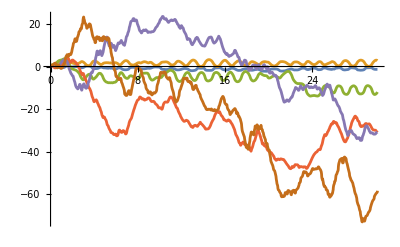

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t]}/. s],{t,0,30},PlotStyle->Automatic,PlotRange->All]
```

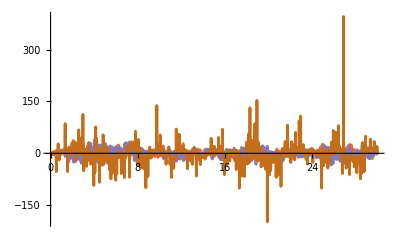

```mathematica
Plot[Evaluate[{θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t]}/. s],{t,0,30},PlotStyle->Automatic,PlotRange->All]
```